```mathematica
This page is similar to previos page but in one structure.And in this page I will compare the projectile-motion-graph with and without DRAG-FORCE.
```

```mathematica
Clear[m,v,b,g,θ]
```

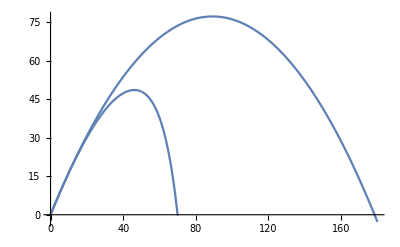

```mathematica
m=0.14;
v=45;
θ=π/3;
g=9.829878576;
b=0.033;
se1=Plot[(g m^2 Log[1-(b h Sec[θ])/(m v)])/b^2+(g h m Sec[θ])/(b v)+h Tan[θ],{h,0,50}];
se2=Plot[1/b^2(m (b v Sin[θ]+g m (1-Log[1-(b h Sec[θ])/(m v)]-2 Log[1+(b v Sin[θ])/(g m)]+(g m^2 v Cos[θ])/((b h-m v Cos[θ]) (g m+b v Sin[θ]))))),{h,50,70}];
co=Plot[Tan[θ]*h-g*h^2/(2*(v*Cos[θ])^2),{h,0,180}];
Show[{se1,se2,co}, PlotRange->Full]
```